```mathematica
ClearAll;
SetDirectory[NotebookDirectory[]];
strm=OpenWrite["output.log"];
$Output={strm};

SetOptions[EvaluationNotebook[],CellEvaluationFunction->(ToExpression[#,StandardForm,Function[Null,Module[{aborted=$Aborted},Internal`WithLocalSettings[Null,aborted=(ReleaseHold[Most[Hold[##]]];Last[Hold[##]]),AbortProtect[If[aborted===$Aborted,Print["Did cleanup"];Abort[]]]]],HoldAll]]&)];
```

```mathematica
(*Needs["IGraphM`"]*)

(*g=IGWeightedAdjacencyGraph[capturedFromPSO]*)
<<IGraphM``
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
(*2 nd De Jong,Rosenbrock' s Saddle function*)
fun1[x_]:=Module[{l=Length@x},
Sum[(1-x[[i]])^2+100 * (x[[i+1]]-x[[i]]^2)^2,{i, l-1} ]
];
Plot[fun1@{x,5},{x,-5,5}]
Plot3D[fun1@{x1, x2}, {x1,-2,2}, {x2, -2,2}]
```

-Graphics3D-

```mathematica
(*Sphere Function*)
fun2[x_]:=Module[{l=Length@x},
Sum[x[[i]]^2,{i,l}]
];
Plot[fun2@{x,5},{x,-5,5}]
Plot3D[fun2@{x1, x2}, {x1,-2,2}, {x2, -2,2}]
```

-Graphics3D-

```mathematica
(*3 rd De Jong*)
fun3[x_]:=Module[{l=Length@x}, Sum[x[[i]], {i,l}]];
Plot[fun3@{x},{x,-5,5}]
Plot3D[fun3@{x1, x2},{x1,-5,5}, {x2, -5,5}]
```

-Graphics3D-

```mathematica
(*Schwefel' s Function*)
fun4[x_]:=Module[{l=Length@x}, Sum[-x[[i]] Sin[Sqrt[Abs[x[[i]]]]], {i,l}]];
Plot[fun4@{x},{x,-420.969,420.969}]
Plot3D[fun4@{x1,x2},{x1,-420.969,420.969},{x2,-420.969,420.969}]
```

-Graphics3D-

```mathematica
(*Rastrigin Function*)
fun5[x_]:=Module[{l=Length@x}, 2*l*(Sum[x[[i]]^2 - 10 * Cos[2 * Pi * x[[i]] ],{i,l}])];
Plot[fun5@{x},{x,-5,5}]
Plot3D[fun5@{x1,x2}, {x1, -5,5}, {x2,-5,5}]
```

-Graphics3D-

```mathematica
(*Ackley' s Function 1*)
fun6[x_]:=Module[{l=Length@x}, Sum[(ⅇ^-5* Sqrt[x[[i]]^2  +  x[[i+1]]^2])  + 3 * ( Cos[2* x[[i]] ] +  Sin[2 * x[[i+1]]]),{i,l-1}]];
Plot[fun6@{x,2},{x,-5,5}]
Plot3D[fun6@{x1,x2},{x1,-5,5},{x2,-5,5}]
```

-Graphics3D-

```mathematica
(*Ackley' s Function 2*)
fun7[x_]:=Module[{l=Length@x},Sum [20  +  ⅇ  -  (20/ ⅇ^(0.2Sqrt[(x[[i]]^2   +  x[[i+1]]^2)/2]))  -  ⅇ^(0.5  * (  Cos[2 * Pi * x[[i]]]  +   Cos[2 *  Pi  *  x[[i+1]]])), {i, l-1}]];
Plot[fun7@{x,5}, {x,-5,5}]
Plot3D[fun7[{x1,x2}], {x1, -5,5}, {x2,-5,5}]
```

-Graphics3D-

```mathematica
Clear[inertia];
Clear[swarmPosition];
Clear[swarmVelocity];
Clear[pBestPosition];
Clear[pBestCost];
Clear[swarmPositionCostTemp];
Clear[swarmPositionTemp];
Clear[swarmPositionCost];
Clear[gBestPosition];
Clear[gBestCost];
Clear[boundry];
Clear[historyGBestCost];
Clear[historyGBestPosition];

Clear[f];
Clear[fLowerBound];
Clear[fUpperBound];
Clear[swarmDim];
Clear[NP];
Clear[c1];
Clear[c2];
Clear[w];
Clear[iterations];
```

```mathematica
draw[matrix_]:=Module[{f,g,adjacencyMatrix,vertices},
adjacencyMatrix=matrix;
adjacencyMatrix=Rescale@adjacencyMatrix/. 0->∞//N;
f[pts_List,e_]:=Block[
{s=0.015,weight=PropertyValue[{g,e},EdgeWeight]},
{
ColorData["TemperatureMap"][weight],
Arrowheads[{{s,0.1},{s,0.9}}],
AbsoluteThickness[weight*15],
Arrow[pts]
}
];

vertices=Join[{{0,0}},Table[{4 Cos[a],4 Sin[a]},{a,Pi/4,2 Pi,Pi/4}],Table[{7 Cos[a],7 Sin[a]},{a,0,5 Pi/3,Pi/6}]][[1;;Length@adjacencyMatrix]];
g=WeightedAdjacencyGraph[adjacencyMatrix,
VertexLabels->"Name",
EdgeLabels->(*"EdgeWeight"*)None,
EdgeShapeFunction->f,
VertexLabelStyle->Directive[Black,Bold,20],
ImageSize->Large,
Background->GrayLevel@0.8,
VertexCoordinates->vertices
(*,
VertexCoordinates->vertices*)
];
Return@g;
];
```

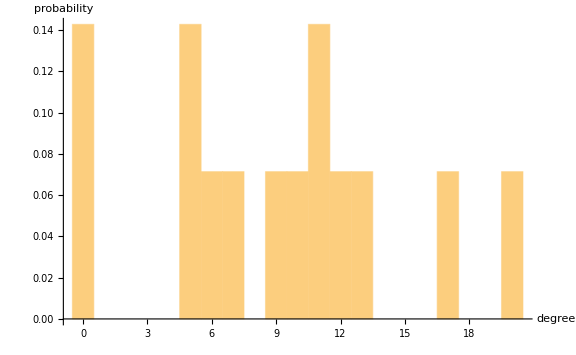

```mathematica
realData={
	{18,5,2,  4 ,   9,  0,  0,  5, 0, 3,   1,   5,    0,   0},
	{  3,6,0,  2 ,   2,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  1,3,3,  4 ,   3,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  9,0,0, 68,  25,  0,  0,  0, 0, 6,  12,   0,   6,    0},
	{19,4,1,57, 139,  0,  0, 0, 0, 7,  62,  0,  44,  0},
	{  1,0,0,  0 ,   0,  5,  4,  0, 0,  0,   0,    0,   0,   0},
	{  1,0,0,  0 ,   0,  3,  2,  0, 0,  0,   0,    0,   0,   0},
	{  6,0,0,  0 ,   1,  0,  0,  2, 0,  0,   0,    3,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  8,2,0,44 , 85, 0,  0,  0, 0,  4,  53,   0,  35,  0},
	{  8,1,0,  0 ,   1,  1,  0,  2, 0,  0,   0,    6,   0,   0},
	{  1,0,0, 25 , 59,  0,  0, 0, 0,  1,  47,   0,  37,  0},
	{  0,0,0,  0 ,   0,   0,  0,  0, 0,  0,    0,    0,   0,   0} };
realData=realData[[All,1;;Length@realData]];
g1=draw@realData
Histogram[VertexDegree[g1],{1},"Probability",AxesLabel->{"degree","probability"}]
```

```mathematica
pts[m_,r_]:=Module[{pts,DCr, DCm, CCr,CCm,BCm, BCr, EVCr, EVCm, ICr, ICm},
pts=0;

DCm = Mean[DegreeCentrality@IGWeightedAdjacencyGraph@m];
DCr = Mean[DegreeCentrality@IGWeightedAdjacencyGraph@r];

CCm=Mean[ClosenessCentrality@IGWeightedAdjacencyGraph@m];
CCr=Mean[ClosenessCentrality@IGWeightedAdjacencyGraph@r];

BCm=Mean[IGBetweenness@IGWeightedAdjacencyGraph@m];
BCr=Mean[IGBetweenness@IGWeightedAdjacencyGraph@r];

EVCm=Mean[IGEigenvectorCentrality@WeightedAdjacencyGraph@m];
EVCr=Mean[IGEigenvectorCentrality@WeightedAdjacencyGraph@r];
(*Information centrality*)
pts=((DCr-DCm)/DCr)^2+((CCr-CCm)/CCr)^2+((BCr-BCm)/BCr)^2+((EVCr-EVCm)/EVCr)^2;
pts*=1000;
Return@pts
];
```

```mathematica
PSOAlgorithmInner[f_, fLimit_, swarmDim_, NP_, c1_, c2_, w_, iterations_
]:=Module[
{
inertia,swarmPosition,swarmPositionTemp,swarmVelocity,pBestPosition,
pBestCost,swarmPositionCost,swarmPositionCostTemp,gBestPosition,gBestPositionIndex,
gBestCost,FitnessFunction,fLowerBound,fUpperBound,f1,
rand1,
rand2,
i,j,k,n,l,
boundry,
historyGBestPosition,historyGBestCost,communicationList,
it,
(*new parameters*)
capturedDataFromPSO, sortedCapturedDataFromPSO,
matrixFormSortedCapturedDataFromPSO, testList,
capturedFromPSO, subList, g1, ptsHistory
},

inertia=ConstantArray[0,{NP,swarmDim}];
swarmPosition=ConstantArray[0,{NP,swarmDim}];
swarmPositionTemp={};
swarmVelocity=ConstantArray[0,{NP,swarmDim}];
pBestPosition=ConstantArray[0,{NP,swarmDim}];
pBestCost=Table[0,NP];
swarmPositionCostTemp=Table[0,swarmDim];
swarmPositionCost=Table[0,NP];
swarmPositionCostTemp=0;
gBestPosition=Table[0,swarmDim];
gBestCost=0;
gBestPositionIndex;
FitnessFunction=f;
f1=FitnessFunction;
fLowerBound=fLimit[[1]];
fUpperBound=fLimit[[2]];
boundry={};
historyGBestPosition={};
historyGBestCost={};
communicationList={};

(*new parameters*)
capturedDataFromPSO={};
sortedCapturedDataFromPSO = {};
matrixFormSortedCapturedDataFromPSO={};
testList={};
capturedFromPSO={};
ptsHistory={};

(*Initialization start*)
swarmPosition=RandomReal[{fLowerBound,fUpperBound},{NP,swarmDim}];
swarmVelocity=ConstantArray[0,{NP,swarmDim}];
pBestPosition=swarmPosition;
f1[x__]:=Re[Map[FitnessFunction,{x}]];

swarmPositionCost=Table[f1[swarmPosition[[n]]],{n,NP}];
pBestCost=swarmPositionCost;
gBestCost=Min[pBestCost];
gBestPosition=pBestPosition[[First@First@Position[swarmPositionCost,gBestCost]]];
gBestPositionIndex=First@First@Position[swarmPositionCost,gBestCost];
(*Initial communication*)
(*communicationList = {First@First@Position[swarmPosition, pBestPosition[[i]] ]<-> gBestPositionIndex}; 
Print[First@First@Position[swarmPosition, pBestPosition[[i]] ]<-> gBestPositionIndex];*)
For[l=1,l<=Length@swarmPosition,l++,
If[l== gBestPositionIndex, Continue[]];(*This is to avoid double connection between gBest and current particle position*)
	AppendTo[communicationList, gBestPositionIndex <-> l];
];
(*Main Loop*)

it=0;
While[it< iterations,
{

(*Update the velocity and position vectors*)
For[i=1,i≤  (NP),i++,
For[j=1,j≤  (swarmDim),j++,
rand1=RandomReal[{0,1}];
rand2=RandomReal[{0,1}];
inertia=w*swarmVelocity[[i]][[j]];
swarmVelocity[[i]]= inertia + (c1 * rand1 * (pBestPosition[[i]][[j]]- swarmPosition[[i]][[j]]))+
(c2 *rand2 * (gBestPosition - swarmPosition[[i]][[j]]));
];

(*Update the particle's position*)
swarmPosition[[i]] +=swarmVelocity[[i]];
For[j=1,j<=swarmDim,j++,
If[swarmPosition[[i,j]]<fLowerBound,swarmPosition[[i,j]]=RandomReal@fLimit];
If[swarmPosition[[i,j]]>fUpperBound,swarmPosition[[i,j]]=RandomReal@fLimit];
];
n=0;
f1[x__]:=Map[FitnessFunction,{x}];
swarmPositionCost=Table[f1[swarmPosition[[n]]],{n,NP}];

(*Update pBest and gBest*)
If[swarmPositionCost[[i]]<= pBestCost[[i]],
{
pBestCost[[i]]=swarmPositionCost[[i]];
pBestPosition[[i]]=swarmPosition[[i]];
If[pBestCost[[i]]<= gBestCost,
{

AppendTo[communicationList,First@First@Position[swarmPosition, pBestPosition[[i]] ]<-> gBestPositionIndex]; 
For[l=1,l<=Length@swarmPosition,l++,
If[l== gBestPositionIndex, Continue[]];(*This is to avoid double connection between gBest and current particle position*)
	AppendTo[communicationList, i <-> l];
];
gBestCost=pBestCost[[i]];
gBestPosition=pBestPosition[[i]];
gBestPositionIndex=First@First@Position[swarmPosition, pBestPosition[[i]] ];
};
];
}
];
];
AppendTo[historyGBestPosition,gBestPosition];
AppendTo[historyGBestCost,gBestCost];
,it++
}
];
Return@communicationList;
];
```

```mathematica
PSOAlgorithmOuter[ f_,swarmDim_,fLimit_,(*just for inner*)
 NPForInnerPSO_,NPForOuterPSO_,  iterationsForInnerPSO_,iterationsForOuterPSO_,(*both*)
 c1_, c2_, w_, realData_, pts_(*just for outer*)
]:=Module[
{
inertia,swarmPosition,swarmPositionTemp,swarmVelocity,pBestPosition,
pBestCost,swarmPositionCost,swarmPositionCostTemp,gBestPosition,
gBestCost,FitnessFunction,fLowerBound,fUpperBound,f1,
rand1,
rand2,
i,j,k,n,y,o,m,p,
boundry,
historyGBestPosition,historyGBestCost,
it, particlePositionCost,
(*new parameters*)
c1Parameter, c2Parameter, wParametere ,communicationList,
capturedDataFromPSO, sortedCapturedDataFromPSO,
matrixFormSortedCapturedDataFromPSO, testList,
capturedFromPSO, subList, g1, ptsHistory,
c1LowerLimit,
c1UpperLimit, c2LowerLimit,c2UpperLimit,
wLowerLimit, wUpperLimit,
c1Limit,c2Limit,wLimit
},

inertia=ConstantArray[0,{NPForOuterPSO,3}];
swarmPosition=ConstantArray[0,{NPForOuterPSO,3}];
swarmPositionTemp={};(*check usage*)
swarmVelocity=ConstantArray[0,{NPForOuterPSO,3}];
pBestPosition=ConstantArray[0,{NPForOuterPSO,3}];
pBestCost=Table[0,NPForOuterPSO];
swarmPositionCostTemp=Table[0,3];(*check usage*)
swarmPositionCost=Table[0,NPForOuterPSO];
swarmPositionCostTemp=0;
gBestPosition=Table[0,3];
boundry={};
historyGBestPosition={};
historyGBestCost={};
(*fLowerBound=fLimit[[1]];
fUpperBound=fLimit[[2]];*)

(*Initialization start*)
(*swarmPosition = RandomReal[{0,1},{NP,3}];*)(*Initialization of the population for c1, c2 and w*)
(*initializing the c1 in the range *)

c1Parameter = RandomReal[{0.5,2},{NPForOuterPSO,1}];
c1Parameter=Flatten@c1Parameter;
c1LowerLimit=1;
c1UpperLimit=1.5;
c1Limit={c1LowerLimit,c1UpperLimit};
c2Parameter = RandomReal[{0.5,2},{NPForOuterPSO,1}];
c2Parameter=Flatten@c2Parameter;
c2LowerLimit=1;
c2UpperLimit=1.5;
c2Limit={c2LowerLimit, c2UpperLimit};
wParametere = RandomReal[{0.4,0.9},{NPForOuterPSO,1}];
wParametere=Flatten@wParametere;
wLowerLimit=0;
wUpperLimit=1;(*later make as input parameter to method*)
wLimit={wLowerLimit,wUpperLimit};

(*new parameter initialization here*)
capturedDataFromPSO={};
sortedCapturedDataFromPSO = {};
matrixFormSortedCapturedDataFromPSO={};
testList={};
capturedFromPSO={};
ptsHistory={};
particlePositionCost=0;

For[o=1,o<=NPForOuterPSO,o++,
swarmPosition[[o]]={c1Parameter[[o]], c2Parameter[[o]],wParametere[[o]]};
];
Print["swarm parameters at initialization:", swarmPosition];

(*
	swarmPosition  = {c1Random,c2Random,wRandom};(*3x5*)
	swarmPosition=Transpose[swarmPosition];(*5x3*)
*)

(*Print["Initialization of c1, c2 and w in outer PSO", swarmPosition];
Print["c1, c2 and w are in the range from 0 to 1"];*)
(*swarmVelocity=ConstantArray[0,{NP,swarmDim}];*)
pBestPosition=swarmPosition;
(*Print["Call to inner PSO: For each set of c1, c2 and w, the innerPSO finds the gBest and return to outerPSO"];*)
(*PSOAlgorithmInner[f_, fLimit_, swarmDim_, NP_, c1_, c2_, w_, iterations_*)
For[y=1,y<= NPForOuterPSO, y++,
communicationList = PSOAlgorithmInner[f,fLimit ,swarmDim,NPForInnerPSO,swarmPosition[[y]][[1]],swarmPosition[[y]][[2]],swarmPosition[[y]][[3]], iterationsForInnerPSO];
(*Print["Output from inner PSO outside loop= ",communicationList];*)
capturedDataFromPSO=communicationList;
sortedCapturedDataFromPSO = Sort[capturedDataFromPSO,#1[[1]]<#2[[1]]&];
(*Print["sortec communicationList outside loop= ",sortedCapturedDataFromPSO];*)
matrixFormSortedCapturedDataFromPSO = AdjacencyMatrix@capturedDataFromPSO //MatrixForm;
testList=AdjacencyMatrix@sortedCapturedDataFromPSO;
(*Print["sorted communicationList outside loop= ",sortedCapturedDataFromPSO];*)
capturedFromPSO={};
For[m=1,m<=Length@testList,m++,
subList={};
For[p=1,p<=Length@testList,p++,
AppendTo[subList, testList[[m]][[p]]];
];
AppendTo[capturedFromPSO, subList];
];
capturedFromPSO=capturedFromPSO[[All,1;;Length@capturedFromPSO]];
(*Print["capturedfrom PSO outside loop= ",capturedFromPSO];*)
(*AppendTo[ptsHistory, pts[capturedFromPSO,realData]];*)
particlePositionCost =pts[capturedFromPSO,realData];
(*Print["result from pts outside loop= ",particlePositionCost];*)

(*PSOAlgorithmInner[f_, fLimit_, swarmDim_, NP_, c1_, c2_, w_, iterations_*)
(*Print[" Initialization:gBest for this InnerPSO call  from outer",particlePositionCost];*) 
swarmPositionCost[[y]]= particlePositionCost;
(*AppendTo[swarmPositionCost,particlePositionCost];*)
];
(*Print[" Set of pBest for initial values of c1, c2 and w: ",swarmPositionCost];*)
(*swarmPositionCost = Flatten[swarmPositionCost];*)
pBestCost=swarmPositionCost;
gBestCost=Min[pBestCost];

(*Print["gBestCost on Initialization", gBestCost];*)
gBestPosition=pBestPosition[[First@First@Position[swarmPositionCost,gBestCost]]];
(*Print["gBestPosition on Initialization", gBestPosition];*)
(*Print["Initial values gBest for outerPSO", gBestPosition];*)
(*Print["f(x) From OUter- swarmPosition: ",swarmPosition];
Print["x: From OUter - swarmPositionCost",swarmPositionCost];
Print["gBest:From OUter - gBestPosition ",gBestPosition];
Print["f(gBest):From OUter - gBestCost",gBestCost];
Print["Initial gBest position index = ", First@First@Position[swarmPositionCost,gBestCost]];
Print@"----------------------------From OUter";
*)
(*Main Loop*)
it=0;
While[it< iterationsForOuterPSO,
{

(*Update the velocity and position vectors*)
For[i=1,i≤  (NPForOuterPSO),i++,
For[j=1,j≤  swarmDim,j++,
rand1=RandomReal[{0,1}];
rand2=RandomReal[{0,1}];
inertia=w*swarmVelocity[[i]][[j]];
swarmVelocity[[i]]= inertia + (c1 * rand1 * (pBestPosition[[i]][[j]]- swarmPosition[[i]][[j]]))+
(c2 *rand2 * (gBestPosition - swarmPosition[[i]][[j]]));
];

(*Update the particle's position*)
swarmPosition[[i]] +=swarmVelocity[[i]];
(*Print["Swarm position being updated",swarmPosition];*)
For[j=1,j<=NPForOuterPSO,j++,
If[swarmPosition[[i,1]]<c1LowerLimit,swarmPosition[[i,1]]=RandomReal@c1Limit];
If[swarmPosition[[i,1]]>c1UpperLimit,swarmPosition[[i,1]]=RandomReal@c1Limit];

If[swarmPosition[[i,2]]<c2LowerLimit,swarmPosition[[i,2]]=RandomReal@c2Limit];
If[swarmPosition[[i,2]]>c2UpperLimit,swarmPosition[[i,2]]=RandomReal@c2Limit];

If[swarmPosition[[i,3]]<wLowerLimit,swarmPosition[[i,3]]=RandomReal@wLimit];
If[swarmPosition[[i,3]]>fUpperBound,swarmPosition[[i,j]]=RandomReal@wLimit];
];
n=0;

(*PSOAlgorithmInner[f_, fLimit_, swarmDim_, NP_, c1_, c2_, w_, iterations_*)

communicationList = PSOAlgorithmInner[f,fLimit,swarmDim,NPForInnerPSO,swarmPosition[[i]][[1]],swarmPosition[[i]][[2]],swarmPosition[[i]][[3]], iterationsForInnerPSO];
(*Print["Output from inner PSO inside loop = ",communicationList];*)
capturedDataFromPSO=communicationList;
sortedCapturedDataFromPSO = Sort[capturedDataFromPSO,#1[[1]]<#2[[1]]&];
(*Print["sorted communicationList inside loop= ",sortedCapturedDataFromPSO];*)
matrixFormSortedCapturedDataFromPSO = AdjacencyMatrix@capturedDataFromPSO //MatrixForm;
testList=AdjacencyMatrix@sortedCapturedDataFromPSO;
(*Print["testList communicationList inside loop= ",testList];*)
capturedFromPSO={};
For[m=1,m<=Length@testList,m++,
subList={};
For[p=1,p<=Length@testList,p++,
AppendTo[subList, testList[[m]][[p]]];
];
AppendTo[capturedFromPSO, subList];
];
capturedFromPSO=capturedFromPSO[[All,1;;Length@capturedFromPSO]];
(*Print["capturedfrom PSO inside loop= ",capturedFromPSO];*)
particlePositionCost =pts[capturedFromPSO,realData];
(*Print["result from pts inside loop= ",particlePositionCost];*)

(*Print["gBest for this InnerPSO call  from outer",particlePositionCost];*)

swarmPositionCost[[i]] =particlePositionCost;

(*Update pBest and gBest*)
If[swarmPositionCost[[i]]<= pBestCost[[i]],
{
pBestCost[[i]]=swarmPositionCost[[i]];
pBestPosition[[i]]=swarmPosition[[i]];
(*Print@"----Particle improved because of the gBest-------";
Print["pBestCost Improved because of gBest = ", pBestCost[[i]]];
Print["pBestPosition Improved because of gBest= ", pBestPosition[[i]]];
Print["pBest position index Improved because of gBest= ", First@First@Position[swarmPositionCost,pBestCost[[i]]]];*)

If[pBestCost[[i]]<= gBestCost,
{
(*Print@"----Particle updating the gBest From OUter-------";*)
gBestCost=pBestCost[[i]];
gBestPosition=pBestPosition[[i]];
(*Print["gBestCost From OUter = ", pBestCost[[i]]];
Print["gBestPosition From OUter= ", pBestPosition[[i]]];
Print["gBest position index From OUter= ", First@First@Position[swarmPositionCost,pBestCost[[i]]]];*)
};
];
}
];
];
(*Print["gBestCost at ", it ," iteration ", gBestCost];
Print["gBestPosition at ", it ," iteration ", gBestPosition];*)
AppendTo[historyGBestPosition,gBestPosition];
AppendTo[historyGBestCost,gBestCost];
,it++
}];
Return@{gBestPosition, historyGBestPosition, historyGBestCost,swarmPositionCost, swarmPosition};
];
```

```mathematica
(*PSOAlgorithmOuter[ f_,swarmDim_,fLimit_, NPForInnerPSO_,NPForOuterPSO_,  iterationsForInnerPSO_,iterationsForOuterPSO_, c1_, c2_, w_, realData_, pts_];*)
outputFromOuterPSO = PSOAlgorithmOuter[fun4, 3,{-5,5}, 14,30,50,1000 ,1.49445,1.49445,0.729,  realData, pts]
```

{{1.06251,1.3325,1.14173},{{1.18083,1.55909,0.636283},{1.18083,1.55909,0.636283},{1.06251,1.3325,1.14173},{1.06251,1.3325,1.14173},{1.06251,1.3325,1.14173},{1.06251,1.3325,1.14173},{1.06251,1.3325,1.14173},{1.06251,1.3325,1.14173},{1.06251,1.3325,1.14173},{1.06251,1.3325,1.14173}},{1418.32,1418.32,1113.97,1113.97,1113.97,1113.97,1113.97,1113.97,1113.97,1113.97},{6343.29,9899.69,5395.12,6343.29,4372.93,5395.12,8092.14,8092.14,6600.58,8092.14,11673.2,7128.49,5053.86,8122.25,8092.14,9899.69,1925.78,5053.86,6343.29,11673.2,9899.69,11673.2,6343.29,9899.69,6343.29,9899.69,8092.14,6089.56,9899.69,9899.69},{{1.30673,1.4899,0.766667},{1.00609,1.20734,0.880394},{1.31008,1.10568,1.20982},{1.29713,1.33648,1.06334},{1.21474,1.30844,0.531684},{1.04903,1.15254,0.882989},{1.33782,1.48526,1.15787},{1.09855,1.37022,1.1398},{1.16422,1.49791,0.94983},{1.17876,1.49427,0.803221},{1.49731,1.14666,1.1445},{1.20999,1.1632,0.66956},{1.16658,1.14336,0.896397},{1.41823,1.20355,0.369536},{1.2838,1.37712,1.23816},{1.42057,1.02847,0.439932},{1.00071,1.29351,1.01491},{1.10652,1.28869,1.10914},{1.28054,1.09627,0.871148},{1.43761,1.25056,1.15132},{1.37696,1.08161,1.02664},{1.18669,1.19268,1.17666},{1.19233,1.05069,0.916438},{1.01795,1.28282,2.01542},{1.30614,1.35708,1.06443},{1.4349,1.08264,1.06054},{1.03188,1.05559,1.22052},{1.48614,1.48175,1.17885},{1.01754,1.29648,0.455977},{1.21756,1.29307,1.06675}}}

```mathematica
(*Return@{gBestPosition, historyGBestPosition, historyGBestCost,swarmPositionCost, swarmPosition};*)
```

```mathematica
Print["outputFromOuterPSO with considering the all function"];
Print["Complete output from outer PSO : ",outputFromOuterPSO];
```

```mathematica
Print["History of best pts value : ", outputFromOuterPSO[[3]]];
```

```mathematica
Print["Pts values at all positions : ", outputFromOuterPSO[[4]]]
```

```mathematica
Print["Minimum value of pts detected : ", Min@outputFromOuterPSO[[4]]];
```

```mathematica
Print["Position of best pts value particle in the swarm : ", Position[outputFromOuterPSO[[4]], Min@outputFromOuterPSO[[4]]]];
```

```mathematica
Print["all parameters position : ", allParametersPosition =outputFromOuterPSO[[5]]];
resultingParametersForMinPts = allParametersPosition[[First@First@Position[outputFromOuterPSO[[4]], Min@outputFromOuterPSO[[4]]]]]
```

{1.00071,1.29351,1.01491}

```mathematica
Print["Parameters for minimun values of pts : ", allParametersPosition[[First@First@Position[outputFromOuterPSO[[4]], Min@outputFromOuterPSO[[4]]]]]];
```

```mathematica
Print@"----------Section with calculation of min pts using set of test functions---------";
```

```mathematica
(*outputOfOuterPSOWithTestFunctions=ConstantArray[0,{7,5}]*)
```

```mathematica
(*listWithAllMinimumPtsValueForEachFunction = Table[0,7];*)
```

```mathematica
(*functionList={fun1, fun2, fun3, fun4, fun5, fun6, fun7};
functionIndexWhichProducedMinimumPts = 0;
allParametersC1andC2andWPositionForAGivenFunction = ConstantArray[0,{7,3}];
parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction = ConstantArray[0,{7,3}];*)
```

```mathematica
(*For[u=1,u<=7,u++,
(*PSOAlgorithmOuter[ f_,swarmDim_,fLimit_, NPForInnerPSO_,NPForOuterPSO_,  iterationsForInnerPSO_,iterationsForOuterPSO_, c1_, c2_, w_, realData_, pts_];*)
(*Return@{gBestPosition, historyGBestPosition, historyGBestCost,swarmPositionCost, swarmPosition};*)
outputOfOuterPSOWithTestFunctions[[u]]= PSOAlgorithmOuter[functionList[[u]], 3,{-5,5}, 14,14,2,2 ,1.49445,1.49445,0.729,  realData, pts];
allParametersC1andC2andWPositionForAGivenFunction = outputOfOuterPSOWithTestFunctions[[u]][[5]];
parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[u]] = allParametersC1andC2andWPositionForAGivenFunction[[First@First@Position[outputOfOuterPSOWithTestFunctions[[u]][[4]], Min@outputOfOuterPSOWithTestFunctions[[u]][[4]]]]];
listWithAllMinimumPtsValueForEachFunction[[u]]= Min[outputOfOuterPSOWithTestFunctions[[u]][[4]]];
];
functionIndexWhichProducedMinimumPts = Position[listWithAllMinimumPtsValueForEachFunction, Min@listWithAllMinimumPtsValueForEachFunction];

Switch[First@First@functionIndexWhichProducedMinimumPts,
1,
Print@"fun1 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[1]]];
Print[listWithAllMinimumPtsValueForEachFunction[[1]]];
,
2, 
Print@"fun2 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[2]]];
Print[listWithAllMinimumPtsValueForEachFunction[[2]]];
,
3,
Print@"fun3 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[3]]];
Print[listWithAllMinimumPtsValueForEachFunction[[3]]];
,
4,
Print@"fun4 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[4]]];
Print[listWithAllMinimumPtsValueForEachFunction[[4]]];
,
5,
Print@"fun5 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[5]]];
Print[listWithAllMinimumPtsValueForEachFunction[[5]]];
,
6,
Print@"fun6 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[6]]];
Print[listWithAllMinimumPtsValueForEachFunction[[6]]];
,
7,
Print@"fun7 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[7]]];
Print[listWithAllMinimumPtsValueForEachFunction[[7]]];
];*)

functionRange[f_]:=
Switch[f,1,{-5,5},2, {-5,5} , 3, {0,5}, 4, {-5,5}, 5,{-5,5}, 6,{-5,5},7,{-5,5}
];

functionWithBestValueForPts[ fList_,swarmDim_,functionRange_,
 NPForInnerPSO_,NPForOuterPSO_,  iterationsForInnerPSO_,iterationsForOuterPSO_,
 c1_, c2_, w_, realData_, pts_, resultingParametersForMinPts_, PSOAlgorithmOuter_
]:=Module[
{
outputOfOuterPSOWithTestFunctions,
listWithAllMinimumPtsValueForEachFunction,
functionList,
functionIndexWhichProducedMinimumPts,
allParametersC1andC2andWPositionForAGivenFunction,
parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction,u
},
outputOfOuterPSOWithTestFunctions=ConstantArray[0,{7,5}];
listWithAllMinimumPtsValueForEachFunction = Table[0,7];
functionList=fList;
functionIndexWhichProducedMinimumPts = 0;
allParametersC1andC2andWPositionForAGivenFunction = ConstantArray[0,{7,3}];
parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction = ConstantArray[0,{7,3}];
For[u=1,u<=Length@fList,u++,
(*PSOAlgorithmOuter[ f_,swarmDim_,fLimit_, NPForInnerPSO_,NPForOuterPSO_,  iterationsForInnerPSO_,iterationsForOuterPSO_, c1_, c2_, w_, realData_, pts_];*)
(*Return@{gBestPosition, historyGBestPosition, historyGBestCost,swarmPositionCost, swarmPosition};*)
Print["function range for u values =", functionRange[u]];
outputOfOuterPSOWithTestFunctions[[u]]= PSOAlgorithmOuter[functionList[[u]], swarmDim,functionRange[u],NPForInnerPSO,NPForOuterPSO,iterationsForInnerPSO, iterationsForOuterPSO,resultingParametersForMinPts[[1]], resultingParametersForMinPts[[2]], resultingParametersForMinPts[[3]],  realData, pts];
allParametersC1andC2andWPositionForAGivenFunction = outputOfOuterPSOWithTestFunctions[[u]][[5]];
parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[u]] = allParametersC1andC2andWPositionForAGivenFunction[[First@First@Position[outputOfOuterPSOWithTestFunctions[[u]][[4]], Min@outputOfOuterPSOWithTestFunctions[[u]][[4]]]]];
listWithAllMinimumPtsValueForEachFunction[[u]]= Min[outputOfOuterPSOWithTestFunctions[[u]][[4]]];
];
functionIndexWhichProducedMinimumPts = Position[listWithAllMinimumPtsValueForEachFunction, Min@listWithAllMinimumPtsValueForEachFunction];

Switch[First@First@functionIndexWhichProducedMinimumPts,
1,
Print@"fun1 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[1]]];
Print[listWithAllMinimumPtsValueForEachFunction[[1]]];
,
2, 
Print@"fun2 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[2]]];
Print[listWithAllMinimumPtsValueForEachFunction[[2]]];
,
3,
Print@"fun3 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[3]]];
Print[listWithAllMinimumPtsValueForEachFunction[[3]]];
,
4,
Print@"fun4 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[4]]];
Print[listWithAllMinimumPtsValueForEachFunction[[4]]];
,
5,
Print@"fun5 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[5]]];
Print[listWithAllMinimumPtsValueForEachFunction[[5]]];
,
6,
Print@"fun6 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[6]]];
Print[listWithAllMinimumPtsValueForEachFunction[[6]]];
,
7,
Print@"fun7 produced the minimum value of pts";
Print[parametersC1andC2andWWhichProducedMinimumPtsForAGivenFunction[[7]]];
Print[listWithAllMinimumPtsValueForEachFunction[[7]]];
];
];

(* using function functionWithBestValueForPts*)

functionList={fun1, fun2, fun3, fun4, fun5, fun6, fun7};
(*functionWithBestValueForPts[ fList_,swarmDim_,functionRange_,
 NPForInnerPSO_,NPForOuterPSO_,  iterationsForInnerPSO_,iterationsForOuterPSO_,
 c1_, c2_, w_, realData_, pts_
]*)
functionWithBestValueForPts[functionList, 3,functionRange, 14,30,50,1000,resultingParametersForMinPts[[1]],resultingParametersForMinPts[[2]],resultingParametersForMinPts[[3]],  realData, pts,resultingParametersForMinPts, PSOAlgorithmOuter];
(*PSOAlgorithmOuter[ f_,swarmDim_,fLimit_, NPForInnerPSO_,NPForOuterPSO_,  iterationsForInnerPSO_,iterationsForOuterPSO_, c1_, c2_, w_, realData_, pts_];*)
```

```mathematica
Close[strm];
```